# Doubly Periodic Scherk Surface

## Weierstrass Data

```mathematica
phi1[z_]:=ρ/z(z-1)^(-1/2)(z+1)^(1/2);
phi2[z_]:=1/ρ/z(z-1)^(1/2)(z+1)^(-1/2);
```

```mathematica
dh[z_]:=1/z
```

```mathematica
ρ=1;
```

```mathematica
G[z_]:=(√(1+z))/(√(-1+z));
```

```mathematica
ω1[z_] :=-( phi1[z]-phi2[z])/2;
ω2[z_] :=I( phi1[z]+phi2[z] )/2;
ω3[z_]:=dh[z];
```

## Parametrization

```mathematica
Integrate[{ω1[z],ω2[z],ω3[z]},z]
```

{-2 ArcTan[(√(-1+z))/(√(1+z))],2 ⅈ ArcSinh[(√(-1+z))/(√2)],Log[z]}

```mathematica
f[z_]=Re[Integrate[{ω1[z],ω2[z],ω3[z]},z]]
```

{-2 Re[ArcTan[(√(-1+z))/(√(1+z))]],-2 Im[ArcSinh[(√(-1+z))/(√2)]],Re[Log[z]]}

```mathematica
f0[1]
```

{0,0,0}

```mathematica
n[z_]:=StereographicProjection[G[z]]
```

```mathematica
xmin=.015;
nx=10;
ny=10;
```

```mathematica
ϵ=.000000001;
xspec={xmin,1-ϵ};
fff[{x_,y_}]:=ExpNRange[x,y,nx];
XR=Union[Flatten[fff/@Partition[xspec,2,1]],SameTest->AlmostEqual];
YR=NRange[ϵ,Pi-ϵ,ny];
```

```mathematica
dm=PolarDomain[XR,YR];
```

```mathematica
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},dm];
```

```mathematica
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[f[1],f[I]]]];
```

```mathematica
mp3=MeshJoin[mp2,MeshReflect[mp2,Plane[{1,0,0},0]]];
```

```mathematica
mp4=MeshJoin[mp3,MeshReflect[mp3,Plane[{0,1,0},0]]];
```

```mathematica
mp5=MeshJoin[mp4,MeshTranslate[mp4,{2Pi,0,0}]];
```

```mathematica
mp6=MeshJoin[mp5,MeshTranslate[mp5,{0,2Pi,0}]];
```

```mathematica
Show[gr =Mesh3DToGraphicsComplex[mp6,{FaceForm[Pink,LightBlue]}]]
```

-Graphics3D-

## Raytrace

```mathematica
xmin=.015;
nx=30;
ny=30;
ϵ=0.000000001;
xspec={xmin,1-ϵ};
fff[{x_,y_}]:=ExpNRange[x,y,nx];
XR=Union[Flatten[fff/@Partition[xspec,2,1]],SameTest->AlmostEqual];
YR=NRange[ϵ,Pi-ϵ,ny];
xr={xmin,1-ϵ};
yr={ϵ,Pi-ϵ};
```

```mathematica
domain=PolarDomain[XR,YR];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[f[1],f[I]]]];
mp3=MeshJoin[mp2,MeshReflect[mp2,Plane[{1,0,0},0]]];
mp4=MeshJoin[mp3,MeshReflect[mp3,Plane[{0,1,0},0]]];
mp5=MeshJoin[mp4,MeshTranslate[mp4,{2Pi,0,0}]];
mp6=MeshJoin[mp5,MeshTranslate[mp5,{0,2Pi,0}]];
FR0=mp6;

domain=PolarDomain[xr,yr];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[f[1],f[I]]]];
mp3=MeshJoin[mp2,MeshReflect[mp2,Plane[{1,0,0},0]]];
mp4=MeshJoin[mp3,MeshReflect[mp3,Plane[{0,1,0},0]]];
mp5=MeshJoin[mp4,MeshTranslate[mp4,{2Pi,0,0}]];
mp6=MeshJoin[mp5,MeshTranslate[mp5,{0,2Pi,0}]];
FR1=mp6;

domain=PolarDomain[XR,yr];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[f[1],f[I]]]];
mp3=MeshJoin[mp2,MeshReflect[mp2,Plane[{1,0,0},0]]];
mp4=MeshJoin[mp3,MeshReflect[mp3,Plane[{0,1,0},0]]];
mp5=MeshJoin[mp4,MeshTranslate[mp4,{2Pi,0,0}]];
mp6=MeshJoin[mp5,MeshTranslate[mp5,{0,2Pi,0}]];
FR2=mp6;

domain=PolarDomain[xr,YR];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[f[1],f[I]]]];
mp3=MeshJoin[mp2,MeshReflect[mp2,Plane[{1,0,0},0]]];
mp4=MeshJoin[mp3,MeshReflect[mp3,Plane[{0,1,0},0]]];
mp5=MeshJoin[mp4,MeshTranslate[mp4,{2Pi,0,0}]];
mp6=MeshJoin[mp5,MeshTranslate[mp5,{0,2Pi,0}]];
FR3=mp6;

PoVExport["dummy",FR0,FR1,FR3,FR2];
```

## Raytrace with more lines

```mathematica
xmin=.015;
nx=30;
ny=30;
ϵ=0.000000001;
xspec={xmin,1-ϵ};
fff[{x_,y_}]:=ExpNRange[x,y,nx];
XR=Union[Flatten[fff/@Partition[xspec,2,1]],SameTest->AlmostEqual];
YR=NRange[ϵ,Pi-ϵ,ny];
nx=6;
ny=6;
xspec={xmin,1-ϵ};
fff[{x_,y_}]:=ExpNRange[x,y,nx];
xr=Union[Flatten[fff/@Partition[xspec,2,1]],SameTest->AlmostEqual];
yr=NRange[ϵ,Pi-ϵ,ny];
```

```mathematica
domain=PolarDomain[XR,YR];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[f[1],f[I]]]];
mp3=MeshJoin[mp2,MeshReflect[mp2,Plane[{1,0,0},0]]];
mp4=MeshJoin[mp3,MeshReflect[mp3,Plane[{0,1,0},0]]];
mp5=MeshJoin[mp4,MeshTranslate[mp4,{2Pi,0,0}]];
mp6=MeshJoin[mp5,MeshTranslate[mp5,{0,2Pi,0}]];
FR0=mp6;

domain=PolarDomain[xr,yr];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[f[1],f[I]]]];
mp3=MeshJoin[mp2,MeshReflect[mp2,Plane[{1,0,0},0]]];
mp4=MeshJoin[mp3,MeshReflect[mp3,Plane[{0,1,0},0]]];
mp5=MeshJoin[mp4,MeshTranslate[mp4,{2Pi,0,0}]];
mp6=MeshJoin[mp5,MeshTranslate[mp5,{0,2Pi,0}]];
FR1=mp6;

domain=PolarDomain[XR,yr];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[f[1],f[I]]]];
mp3=MeshJoin[mp2,MeshReflect[mp2,Plane[{1,0,0},0]]];
mp4=MeshJoin[mp3,MeshReflect[mp3,Plane[{0,1,0},0]]];
mp5=MeshJoin[mp4,MeshTranslate[mp4,{2Pi,0,0}]];
mp6=MeshJoin[mp5,MeshTranslate[mp5,{0,2Pi,0}]];
FR2=mp6;

domain=PolarDomain[xr,YR];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},domain];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[f[1],f[I]]]];
mp3=MeshJoin[mp2,MeshReflect[mp2,Plane[{1,0,0},0]]];
mp4=MeshJoin[mp3,MeshReflect[mp3,Plane[{0,1,0},0]]];
mp5=MeshJoin[mp4,MeshTranslate[mp4,{2Pi,0,0}]];
mp6=MeshJoin[mp5,MeshTranslate[mp5,{0,2Pi,0}]];
FR3=mp6;

PoVExport["dummy",FR0,FR1,FR3,FR2];
```

## Flat Structures

```mathematica
xmin=.001;
nx=5;
ny=10;
```

```mathematica
ϵ=.0000001;
xspec={xmin,a,1-ϵ};
fff[{x_,y_}]:=ExpNRange[x,y,nx];
XR=Union[Flatten[fff/@Partition[xspec,2,1]],SameTest->AlmostEqual];
YR=NRange[ϵ,Pi-ϵ,ny];
```

```mathematica
Phi1[w_]:=NIntegrate[ϕ1[z],{z,I,w}];
Phi2[w_]:=NIntegrate[ϕ2[z],{z,I,w}]
```

```mathematica
mymesh=Mesh2D[MeshRectangle[XR,YR]];
```

```mathematica
exp[z_]:=Re[z]E^(I Im[z]);
```

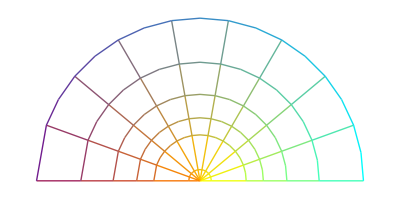

```mathematica
Show[ph1=MeshIntoColorGraphics[AdaptiveMeshApply[Composition[CToR2,exp,R2ToC],mymesh,MaxBend->15],FourInterpolatingCornerColors[Purple,Orange,Yellow,Cyan,mymesh]]]
```

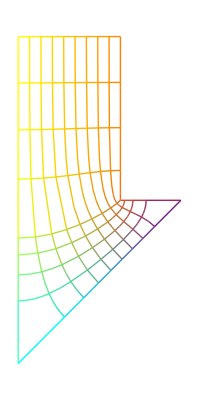

```mathematica
Show[ph1=MeshIntoColorGraphics[AdaptiveMeshApply[Composition[CToR2,Phi1,exp,R2ToC],mymesh,MaxBend->10],FourInterpolatingCornerColors[Purple,Orange,Yellow,Cyan,mymesh]]]
```

```mathematica
Export["ks1.pdf",%]
```

ks1.pdf

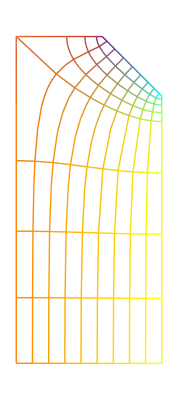

```mathematica
Show[ph2=MeshIntoColorGraphics[AdaptiveMeshApply[Composition[CToR2,Phi2,exp,R2ToC],mymesh,MaxBend->10],FourInterpolatingCornerColors[Purple,Orange,Yellow,Cyan,mymesh]]]
```

```mathematica
Export["ks2.pdf",%]
```

ks2.pdf